```mathematica
(*Code by Amirhossein Rezaei*)
(*Please refrence this code as "Rezaei, A (2020) SymLog (Version 1.1) [Source code],https://github.com/amirh0ss3in/SymLog".*)
ClearAll[ConvertPoint,UnConvertPoint]
ConvertPoint[n_?NumericQ,{down_,up_}]:=Module[{},If[n<0,-ConvertPoint[-n,{-up,-down}],If[n<up,n,Log[n/up]+up]]]
UnConvertPoint[n_?NumericQ,{down_,up_}]:=Module[{},If[n<0,-UnConvertPoint[-n,{-up,-down}],If[n<up,n,Exp[n-up] up]]]

ClearAll[ListSymmetricLogPlot];
ListSymmetricLogPlot[data_List,threshold_?NumericQ,opts:OptionsPattern[]]:=ListSymmetricLogPlot[data,{-threshold,threshold},opts]
ListSymmetricLogPlot[data_List,thresholds:{downthres_,upthres_},opts:OptionsPattern[]]:=Module[{xmin,xmax,ymin,ymax,vticks1,vticks2,vticks3,vticks,vticksright,tmp},{{xmin,xmax},{ymin,ymax}}=CoordinateBounds[data];
vticks1=If[ymin<downthres,tmp=Charting`ScaledTicks[{Log,Exp}][Log[-downthres],Log[-ymin]];
tmp[[All,1]]=Minus@*Exp/@tmp[[All,1]];
tmp[[All,2]]=Replace[tmp[[All,2]],{x_?NumericQ:>-x,_Superscript[a_,b_]:>Superscript[-a,b]},{1}];
tmp,{}];
vticks2=Charting`ScaledTicks["Linear"][downthres,upthres,4];
vticks3=If[ymax>upthres,tmp=Charting`ScaledTicks[{Log,Exp}][Log@upthres,Log@ymax];
tmp[[All,1]]=Exp/@tmp[[All,1]];
tmp,{}];
vticks=vticksright=DeleteDuplicatesBy[SortBy[Join[vticks1,vticks2,vticks3],First],First];
vticksright[[All,2]]="";
ListPlot[data,opts,ScalingFunctions->{None,{ConvertPoint[#,thresholds]&,UnConvertPoint[#,thresholds]&}},PlotRange->All,FrameTicks->{{vticks,vticksright},Automatic},Ticks->{Automatic,vticks}]]
```

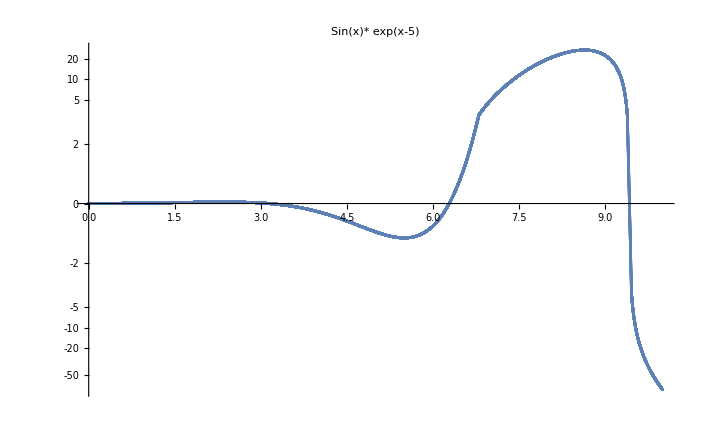

```mathematica
ListSymmetricLogPlot[Table[{x,Sin[x]*Exp[x-5]},{x,0,10,0.0001}],{-3,3},PlotLabel->"Sin(x)* exp(x-5)"]
```